```mathematica
Quit[]
```

```mathematica
ClearAll["Global`*"]
persm:=4 π ϵ[p[r]]pp(r rp)^2(*((1+A)/(1+B))*)(rp/mp)
persp:=(-(GS pp (mp m[r]+4 π pp r^3 rp^3 p[r]) (p[r]+ϵ[p[r]]))/(r rp (r rp-2 GS mp m[r]))(*+(GS^2 lp^2 pp (mp m[r]+4 π pp r^3 rp^3 p[r])^2 (p[r]+ϵ[p[r]]))/(2 r^3 rp^3 (r rp-2 GS mp m[r])^2)*))(rp/pp)
persnu:=2(-(GS pp (mp m[r]+4 π pp r^3 rp^3 p[r]) (-1))/(r rp (r rp-2 GS mp m[r]))(*+(GS^2 lp^2 pp (mp m[r]+4 π pp r^3 rp^3 p[r])^2 (-1))/(2 r^3 rp^3 (r rp-2 GS mp m[r])^2)*))(rp/1)
```

```mathematica
(4*(145)^4)/hbarc^3*10^7
18.076/(8π GS)
```

17682025000000000/hbarc^3

0.719221/GS

```mathematica
Sqrt[0.05]
```

0.223607

#### Run dari sini

```mathematica
ClearAll[rp,mp,pp,GSp,Λ,MSS,c,hbar,GS,lp,r0,rmax,PCC,ϵ,MCC,nuCC,sol,state,w,ϵ0,ϵc,dϵdp,rStar,mStar,rStop,alpha,hbarc,k]
w:=Infinity
ϵ0:=(4*(145)^4)/hbarc^3*10^9
alpha:=10.
lp:=0.001rp (*1.*^-3 rp *) (* > 6.*^-4 rp *)
PCC:=230*10^14
(*PCC:=81 (* mStar==1.405, 0.3 < lp/(r0 rp) < 1 *)*)
(*PCC50:=2 (* mStar==1.827, 0.2 < lp/(r0 rp) < 1 *)*)
(*PCC:=355 (* mStar==1.827, 0.1 < lp/(r0 rp) < 1 *)*)
r0:=alpha lp/rp
rmax:=100000. (* satuan meter *)
(*
Untuk ganti dari satuan NS ke Planck
r->(r rp)
p[r]->(p[r] pp)
m[r]->(m[r] mp)
*)

hbarc:=197.327
rp:=1
mp:=1
pp:=1
GSp:=1

(*rp:=(1.616255 10^-35)^-1
mp:=(2.176435/1.78 10^-23)^-1
pp:=(2.176435/(1.78  (1.616255)^3)10^82)^-1
GSp:=(2.176435*10^12)/(1.78*1.616255)*)

(*Nn=1.43*10^65;*)
MSS:=1.1155 * 10^15*mp (* Massa matahari = 1.1155 * 10^15 MeV m^3/fm^3 = 9.136*10^(37) Planck mass*)
c:=1
hbar:=1
GS:=1.325*10^-12*GSp (* Konstanta gravitasi GS = 1.325*10^-12 fm^3/(MeV m^2)*)
(*lp=N[√((hbar GS)/c^3 Nn/(12 π))];*)

(* Model LinEoS *)
ϵ[p_]:=(*p/w+*)ϵ0;
dϵdp:=D[ϵ[p],p]
(* Model LinEoS *)

MCC:=N[4/3 π r0^3 ϵ[PCC]] (* Massa di pusat *)
nuCC:=0.;
(* Fungsi metrik di pusat *)
```

```mathematica
MCC
```

963965.

```mathematica
rStar=0.;monitor=0.;
(* Method->["EventLocator","Event" :>{Re[p[r]]},"EventAction":>Throw[rStar=r,"StopIntegration"], *)
sol=NDSolve[{m'[r]==persm,p'[r]==persp,nu'[r]==persnu,m[r0]==MCC ,p[r0]==PCC,nu[r0]==nuCC,WhenEvent[p[r]==0,Throw[rStar=r,"StopIntegration"]]},{m,p,nu},{r,r0,rmax},Method->"ExplicitRungeKutta"(*{"EquationSimplification"->"Residual"}*),MaxSteps->10^4,EvaluationMonitor:>(monitor=r)]

monitor
rStar
```

{{m→InterpolatingFunction[{{0.01, 0.589898}}, <>],p→InterpolatingFunction[{{0.01, 0.589898}}, <>],nu→InterpolatingFunction[{{0.01, 0.589898}}, <>]}}

0.589898

0.589898

```mathematica
nuo[r_]=Evaluate[nu[r]/.sol[[1]]];
mo[r_]=Evaluate[m[r]/. sol[[1]]];
po[r_]=Evaluate[p[r]/. sol[[1]]];
Clear[rStop,mStar]
If[rStar==0.,rStop:=monitor;,rStop:=rStar];
mStar=N[mo[rStop]];
ϵc=N[ϵ[PCC]];
```

```mathematica
k=(nuo[rStar]-Log[(1-(2 (GS/GSp) mo[rStar])/(rStar))])
nuo[r_]=nuo[r]-k
```

25.2222

-25.2222+InterpolatingFunction[{{0.01, 0.589898}}, <>][r]

```mathematica
rStop/r0
```

58.9898

```mathematica
r0
rStop
```

0.01

0.589898

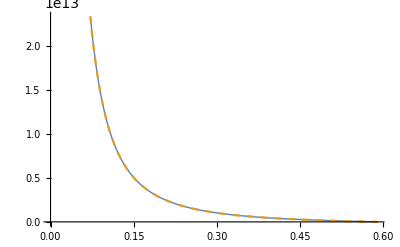

```mathematica
Plot[{po[r],ϵ[PCC]((rStop √(rStop-2 GS mStar)-√(rStop^3-2 GS mStar r^2))/(√(rStop^3-2 GS mStar r^2)-3rStop √(rStop-2 GS mStar)))},{r,r0,rStop},PlotRange->Automatic,PlotStyle->{Thick,Dashed},PlotRange->Full]
```

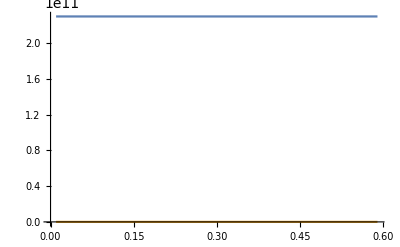

```mathematica
Plot[{Re[ϵ[po[r]]],Im[ϵ[po[r]]]},{r,r0,rStop},PlotRange->Automatic]
```

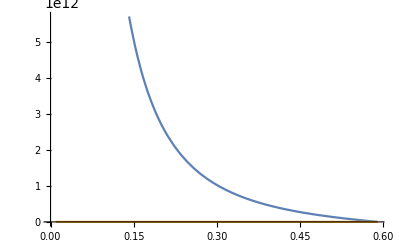

```mathematica
Plot[{Re[po[r]],Im[po[r]]},{r,r0,rStop},PlotRange->Automatic]
```

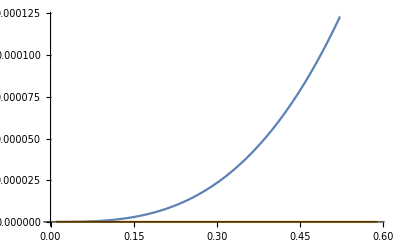

```mathematica
Plot[{Re[mo[r]/MSS],Im[mo[r]/MSS]},{r,r0,rStop},PlotRange->Automatic]
```

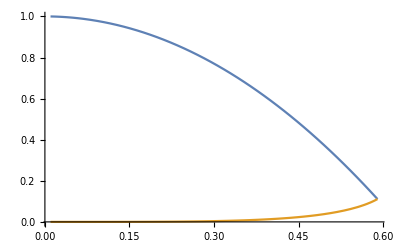

```mathematica
Plot[{(1-(2 (GS/GSp) mo[r])/(r)),Exp[nuo[r]]},{r,r0,rStar}]
```

```mathematica
(2 (GS/GSp) mo[r])/(r)/.{r->rStar}
```

0.888916

```mathematica
(2 (GS/GSp) mo[r])/(r)-N[8/9]/.{r->rStar}
```

0.0000269013

```mathematica
{m[r0]==MCC /MSS,p[r0]==PCC,ρ[r0]==ϵ[PCC]}
{m[rStar]==mo[rStar] /MSS,p[r0]==PCC,ρ[r0]==ϵ[PCC]}
```

{m[0.01]==8.64155×10^-10,p[0.01]==23000000000000000,ρ[0.01]==2.3013×10^11}

{m[0.589898]==0.000177387,p[0.01]==23000000000000000,ρ[0.01]==2.3013×10^11}

HASIL TOV
alpha:=10.
lp:=10.^-3 

saat w=1/3 dan ϵ0=(4*(145)^4)/hbarc^3 dan PC=230 , hasilnya 2Compactness=0.528683<BL
saat w=1 dan ϵ0=(4*(145)^4)/hbarc^3 dan PC=230 , hasilnya 2Compactness=0.658682<BL
saat w=Infinity dan ϵ0=(4*(145)^4)/hbarc^3 dan PC=230 , hasilnya 2Compactness=0.74993<BL

saat w=Infinity dan ϵ0=(4*(145)^4)/hbarc^3 10^9 dan PC=230*10^12 , hasilnya 2Compactness=0.888769<BL
saat w=Infinity dan ϵ0=(4*(145)^4)/hbarc^3 10^9 dan PC=230*10^13 , hasilnya 2Compactness=0.888902>BL
saat w=Infinity dan ϵ0=(4*(145)^4)/hbarc^3 10^9 dan PC=230*10^14 , hasilnya 2Compactness=0.888916>BL

saat w=Infinity dan ϵ0=(4*(145)^4)/hbarc^3 10^8 dan PC=230*10^14 , hasilnya 2Compactness=0.888892 >BL
saat w=Infinity dan ϵ0=(4*(145)^4)/hbarc^3 10^7 dan PC=230*10^14 , hasilnya 2Compactness=0.888889+2.67099×10^-7>BL
saat w=Infinity dan ϵ0=(4*(145)^4)/hbarc^3 10^6 dan PC=230*10^14 , hasilnya 2Compactness=0.888889+2.46995×10^-8>BL

BL(Buchdahl limit) → 2 Compactness = 0.888889

```mathematica
NIntegrate[1/(√(Exp[nuo[r]](1-(2 (GS/GSp) mo[r])/(r)))),{r,r0,rStar}]
```

345.

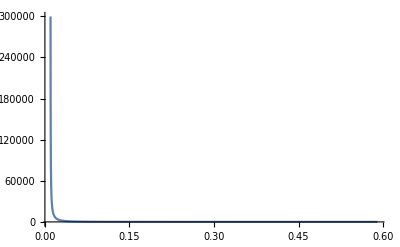

```mathematica
Plot[1/(√(Exp[nuo[r]](1-(2 (GS/GSp) mo[r])/(r)))),{r,r0,rStar},PlotRange->All]
```

#### Run jika hasil numerik sudah benar memenuhi p[R]=0 dan m’[r]>0 untuk 0<r<R

```mathematica
filename=FileNameJoin[{NotebookDirectory[],"profil-vTOV_verif.dat"}]
```

C:\Users\ilham\Dropbox\00 SCGrav\ceknumerik\variasi2\profil-vTOV_verif.dat

```mathematica
Export[filename,Table[{r/1,po[r]*10^-15,(mo[r]mp/MSS)*10^4,(1-(2 (GS/GSp) mo[r])/(r)),Exp[nuo[r]]},{r,r0,rStop,(rStop-r0)/1000}]]
```

C:\Users\ilham\Dropbox\00 SCGrav\ceknumerik\variasi2\profil-vTOV_verif.dat

```mathematica
Solve[√(R^3-2G M δ^2)==3R √(R-2G M),M,]
```

Solve::bdomv: Warning: Null is not a valid domain specification. Assuming it is a variable to eliminate.

{{M→(4 R^3)/(G (9 R^2-δ^2))}}

```mathematica
M->Series[(4 R^3)/(G (9 R^2-δ^2)),{δ,0,10}]
```

M→(4 R)/(9 G)+(4 δ^2)/(81 G R)+(4 δ^4)/(729 G R^3)+(4 δ^6)/(6561 G R^5)+(4 δ^8)/(59049 G R^7)+(4 δ^10)/(531441 G R^9)+O[δ]^11

#### Coba integrasi biar dapet r*

```mathematica
f[r_]:=1/(√(Exp[nuo[r]](1-(2 (GS/GSp) mo[r])/(r))))
n:=1000
x[i_]:=r0+i/n(rStar-r0)
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"TOV-rstar.dat"}],Table[{x[j],rStar+2 GS mo[rStar] Log[rStar/(2 GS mo[rStar])-1]-Sum[(rStar-r0)/(2n)(f[x[i]]+f[x[i-1]]),{i,j,n}]},{j,1,n,1}]]
```

C:\Users\ilham\Dropbox\00 SCGrav\ceknumerik\variasi2\TOV-rstar.dat

```mathematica
datarstar=ReadList[FileNameJoin[{NotebookDirectory[],"TOV-rstar.dat"}],{Number,Number}];
```

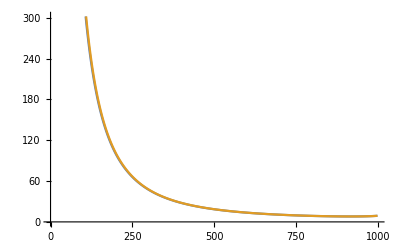

```mathematica
ListLinePlot[{Table[{j,f[datarstar[[j+1,1]]]},{j,2,n-1}],Table[{j,(datarstar[[j+1,2]]-datarstar[[j,2]])/(datarstar[[j+1,1]]-datarstar[[j,1]])},{j,2,n-1}]}]
```

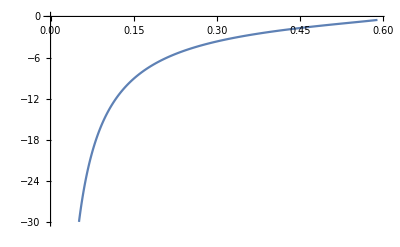

```mathematica
ListLinePlot[datarstar]
```

```mathematica
rStar+2 GS mo[rStar] Log[rStar/(2 GS mo[rStar])-1]
```

-0.500641